# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
Print[Length@uapprox,Length@uvc];
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

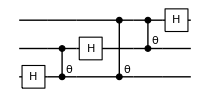

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→3,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.999,EFSingle→{1,0},RabiFreq→10,FidTwo→0.999,EFTwo→{1,0},TwoGateFreq→10}

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
```

```mathematica
varMeanInitStates[conf]
```

<|1→{0.400584,0.481403},2→{0.155551,0.0725884},3→{0.400584,0.481403},4→{0.63785,0.117328}|>

```mathematica
HPsummary@conf
```

{ansatzspace→{0,1,2},connectivity→-Graphics-,dθ→1/100000,fixansatz→{},fixansatzparams→<||>,gateset→<|1→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&},2→{C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>,globalconverge→3,grad→NG,gradstep→0.01,gradstepmultiply→2,greedflat→1/1000,greediness→8,greedinessinit→8,groundstate→0,iterconverge→10,maxbfiter→20,maxgreediter→200,maxpruneiter→300,metignore→1/1000,ngatesinit→24,nqubit→3,parallel→Automatic,perfectingflat→1/10000,pruningerror→0.1,speedupfirst→True,swapfabricdepth→0,usecorr→True,weightgate→{1→0.5,2→0.5},αtikhonov→1/1000,ϵfin→1/100000,θinitrange→0.1,ρinit→<|1→0,2→1,3→2,4→3|>}

Compilation with automatically generated ansatz

InsertCircuitNoise::error: «351»

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

SimplifyCircuit::error: Invalid arguments. See ?SimplifyCircuit

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

General::stop: Further output of ApplyCircuit::error will be suppressed during this calculation.

InsertCircuitNoise::error: «351»

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

SimplifyCircuit::error: Invalid arguments. See ?SimplifyCircuit

InsertCircuitNoise::error: «352»

General::stop: Further output of InsertCircuitNoise::error will be suppressed during this calculation.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

General::stop: Further output of ExtractCircuit::error will be suppressed during this calculation.

SimplifyCircuit::error: Invalid arguments. See ?SimplifyCircuit

General::stop: Further output of SimplifyCircuit::error will be suppressed during this calculation.

@cycle1:Wed 7 Sep 2022 16:21:00, fev:265, <E>: 0.23198681342954736 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 0, 8}

@cycle2:Wed 7 Sep 2022 16:21:26, fev:423, <E>: 0.14195902982375186 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 23, 0, 0, 16}

@cycle3:Wed 7 Sep 2022 16:22:25, fev:650, <E>: 0.12358873632346326 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 31, 0, 0, 19}

@cycle4:Wed 7 Sep 2022 16:23:38, fev:980, <E>: 0.10060030759215066 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 39, 0, 0, 24}

@cycle5:Wed 7 Sep 2022 16:24:35, fev:1191, <E>: 0.08885061311679328 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 50, 0, 0, 28}

I'm slowing down @cycle 6

@cycle6:Wed 7 Sep 2022 16:24:37, fev:1287, <E>: 0.08885061311679328 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 50, 0, 0, 31}

I'm slowing down @cycle 7

@cycle7:Wed 7 Sep 2022 16:24:42, fev:1383, <E>: 0.08885061311679328 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 50, 0, 0, 43}

I'm slowing down @cycle 8

@cycle8:Wed 7 Sep 2022 16:25:36, fev:1479, <E>: 0.08885061311679328 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 50, 0, 0, 58}

{C_1[Rx_0[11.0402]],Depol_2[1.82171×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000303526],Rz_2[11.0688],Depol_0[1.7876×10^-7],Depol_1[1.7876×10^-7],Depol_2[0.0015],Deph_0[0.000297844],Deph_1[0.000297844],Rz_1[10.1908],Depol_0[2.83567×10^-7],Depol_2[2.83567×10^-7],Depol_1[0.0015],Deph_0[0.000472388],Deph_2[0.000472388],Ry_2[1.58343],Depol_0[1.89008×10^-7],Depol_1[1.89008×10^-7],Depol_2[0.0015],Deph_0[0.000314914],Deph_1[0.000314914],C_1[Ry_0[9.89684]],Depol_2[3.18651×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000530804],C_0[Ry_1[2.83218]],Depol_2[3.38066×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000563127],C_0[Rx_1[3.10458]],Depol_2[3.70581×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000617255],Rx_1[10.9117],Depol_0[1.97511×10^-7],Depol_2[1.97511×10^-7],Depol_1[0.0015],Deph_0[0.000329076],Deph_2[0.000329076],Rx_0[11.1913],Depol_1[1.64138×10^-7],Depol_2[1.64138×10^-7],Depol_0[0.0015],Deph_1[0.000273488],Deph_2[0.000273488],Rz_1[11.9112],Depol_0[7.82063×10^-8],Depol_2[7.82063×10^-8],Depol_1[0.0015],Deph_0[0.000130327],Deph_2[0.000130327]}

6464

compile time:5.72604 minutes; total iterations 1688

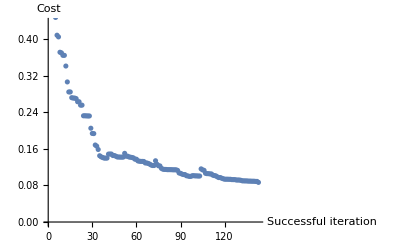

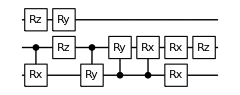

prob(0):<|0→0.331883,1→0.336003,2→0.332114|>

dist_fid=0.120055

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

Compilation with automatically generated ansatz

@cycle1:Wed 7 Sep 2022 14:42:34, fev:349, <E>: 0.19596244272261826 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 8}

@cycle2:Wed 7 Sep 2022 14:47:37, fev:705, <E>: 0.1229680583247173 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 2, 9}

@cycle3:Wed 7 Sep 2022 14:51:09, fev:955, <E>: 0.05900098963338604 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 2, 11}

I'm slowing down @cycle 4

@cycle4:Wed 7 Sep 2022 14:53:12, fev:1051, <E>: 0.05900098963338604 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 2, 14}

I'm slowing down @cycle 5

@cycle5:Wed 7 Sep 2022 14:56:10, fev:1145, <E>: 0.05900098963338604 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 2, 18}

I'm slowing down @cycle 6

@cycle6:Wed 7 Sep 2022 15:01:57, fev:1259, <E>: 0.05900098963338604 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 2, 24}

{C_1[Ry_2[0.350561]],Depol_0[4.18452×10^-8],Depol_(1,2)[0.00125],Deph_0[0.0000697371],Rx_0[0.732455],Depol_1[8.74304×10^-8],Depol_2[8.74304×10^-8],Depol_0[0.0015],Deph_1[0.000145696],Deph_2[0.000145696],Rx_2[1.89392],Depol_0[2.2607×10^-7],Depol_1[2.2607×10^-7],Depol_2[0.0015],Deph_0[0.000376642],Deph_1[0.000376642],C_1[Ry_2[10.0142]],Depol_0[3.04644×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000507483],C_2[Ry_1[10.8079]],Depol_0[2.09901×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000349713],C_0[Rx_1[9.44294]],Depol_2[3.72831×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000621],C_1[Rx_0[6.76925]],Depol_2[6.9198×10^-7],Depol_(0,1)[0.00125],Deph_2[0.00115197],Rx_0[11.6661],Depol_1[1.07467×10^-7],Depol_2[1.07467×10^-7],Depol_0[0.0015],Deph_1[0.00017908],Deph_2[0.00017908],C_2[Rx_1[9.71706]],Depol_0[3.40111×10^-7],Depol_(1,2)[0.00125],Deph_0[0.00056653],C_1[Rx_0[9.07338]],Depol_2[4.16945×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000694426],Ry_2[0.789774],Depol_0[9.42723×10^-8],Depol_1[9.42723×10^-8],Depol_2[0.0015],Deph_0[0.000157096],Deph_1[0.000157096],Ry_0[1.59388],Depol_1[1.90255×10^-7],Depol_2[1.90255×10^-7],Depol_0[0.0015],Deph_1[0.000316991],Deph_2[0.000316991],C_1[Rx_0[3.02096]],Depol_2[3.60601×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000600641],C_1[Rx_2[10.7823]],Depol_0[2.1296×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000354808],C_0[Rx_1[9.24583]],Depol_2[3.9636×10^-7],Depol_(0,1)[0.00125],Deph_2[0.000660164],C_0[Rx_1[6.22349]],Depol_2[7.42874×10^-7],Depol_(0,1)[0.00125],Deph_2[0.00123659],C_1[Rx_2[3.77852]],Depol_0[4.51028×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000751148],C_2[Rx_1[10.5159]],Depol_0[2.44754×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000407757],C_2[Ry_1[11.6198]],Depol_0[1.12987×10^-7],Depol_(1,2)[0.00125],Deph_0[0.000188277],C_1[Rz_0[0.82596]],Depol_2[9.85918×10^-8],Depol_(0,1)[0.00125],Deph_2[0.000164293],C_1[Rz_2[0.569744]],Depol_0[6.80082×10^-8],Depol_(1,2)[0.00125],Deph_0[0.000113334],Rx_2[12.0423],Depol_0[6.25542×10^-8],Depol_1[6.25542×10^-8],Depol_2[0.0015],Deph_0[0.000104246],Deph_1[0.000104246]}

6464

compile time:27.3492 minutes; total iterations 1584

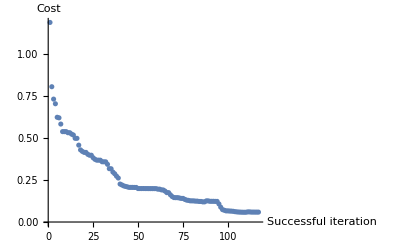

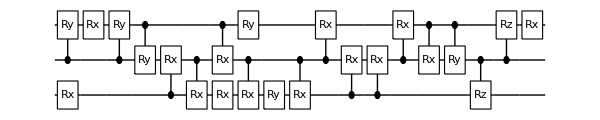

prob(0):<|0→0.332473,1→0.335021,2→0.332506|>

dist_fid=0.115208

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

Compilation with automatically generated ansatz

@cycle1:Tue 6 Sep 2022 10:15:23, fev:303, <E>: 0.41928043413207183 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 0, 1}

@cycle2:Tue 6 Sep 2022 10:15:56, fev:517, <E>: 0.1642344095745596 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 0, 3}

@cycle3:Tue 6 Sep 2022 10:16:39, fev:780, <E>: 0.07842436507037648 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 0, 8}

@cycle4:Tue 6 Sep 2022 10:17:05, fev:923, <E>: 0.07102664466917719 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 22, 0, 0, 11}

@cycle5:Tue 6 Sep 2022 10:17:51, fev:1217, <E>: 0.027263845872166736 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 32, 0, 2, 11}

@cycle6:Tue 6 Sep 2022 10:18:26, fev:1411, <E>: 1.7977100444654948e-6 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 2, 14}

Dot::dotsh: Tensors {-0.197429-0.293603 ⅈ,-0.197189-0.293805 ⅈ,-0.196883-0.293207 ⅈ,-0.196643-0.293408 ⅈ,-0.196581-0.293515 ⅈ,-0.196341-0.293717 ⅈ,-0.196738-0.294172 ⅈ,-0.196497-0.294374 ⅈ} and {1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),«54»} have incompatible shapes.

Dot::dotsh: Tensors {-0.196869-0.294477 ⅈ,0.19659+0.294622 ⅈ,0.293639-0.195611 ⅈ,-0.293783+0.195334 ⅈ,0.294129-0.196221 ⅈ,-0.294274+0.195943 ⅈ,-0.196358-0.294134 ⅈ,0.19608+0.29428 ⅈ} and {1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),«54»} have incompatible shapes.

Dot::dotsh: Tensors {-0.195799-0.294175 ⅈ,-0.195558-0.294376 ⅈ,0.195956+0.294831 ⅈ,0.195715+0.295032 ⅈ,0.0674775-0.347198 ⅈ,0.0677902-0.347171 ⅈ,-0.0675871+0.346532 ⅈ,-0.0678992+0.346505 ⅈ} and {1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),«54»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

compile time:2.74874 minutes; total iterations 1529

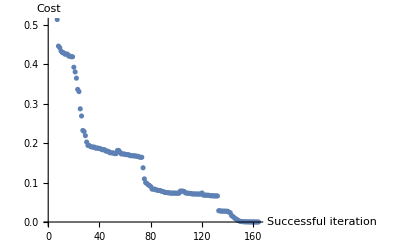

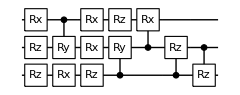

prob(0):<|0→0.332248,1→0.333643,2→0.334109|>

dist_fid=1/8 (Conjugate[{-0.197644-0.293564 ⅈ,-0.197404-0.293766 ⅈ,-0.197097-0.293169 ⅈ,-0.196857-0.293371 ⅈ,0.196697+0.293332 ⅈ,0.196457+0.293533 ⅈ,0.196854+0.293988 ⅈ,0.196614+0.29419 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.197644-0.293564 ⅈ,-0.197404-0.293766 ⅈ,-0.197097-0.293169 ⅈ,-0.196857-0.293371 ⅈ,0.196697+0.293332 ⅈ,0.196457+0.293533 ⅈ,0.196854+0.293988 ⅈ,0.196614+0.29419 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.197429-0.293603 ⅈ,-0.197189-0.293805 ⅈ,-0.196883-0.293207 ⅈ,-0.196643-0.293408 ⅈ,-0.196581-0.293515 ⅈ,-0.196341-0.293717 ⅈ,-0.196738-0.294172 ⅈ,-0.196497-0.294374 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.197429-0.293603 ⅈ,-0.197189-0.293805 ⅈ,-0.196883-0.293207 ⅈ,-0.196643-0.293408 ⅈ,-0.196581-0.293515 ⅈ,-0.196341-0.293717 ⅈ,-0.196738-0.294172 ⅈ,-0.196497-0.294374 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.197106-0.294326 ⅈ,0.196828+0.294472 ⅈ,0.293624-0.195938 ⅈ,-0.293769+0.195661 ⅈ,-0.293968+0.196451 ⅈ,0.294113-0.196173 ⅈ,0.196497+0.293838 ⅈ,-0.196219-0.293983 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.197106-0.294326 ⅈ,0.196828+0.294472 ⅈ,0.293624-0.195938 ⅈ,-0.293769+0.195661 ⅈ,-0.293968+0.196451 ⅈ,0.294113-0.196173 ⅈ,0.196497+0.293838 ⅈ,-0.196219-0.293983 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.196869-0.294477 ⅈ,0.19659+0.294622 ⅈ,0.293639-0.195611 ⅈ,-0.293783+0.195334 ⅈ,0.294129-0.196221 ⅈ,-0.294274+0.195943 ⅈ,-0.196358-0.294134 ⅈ,0.19608+0.29428 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.196869-0.294477 ⅈ,0.19659+0.294622 ⅈ,0.293639-0.195611 ⅈ,-0.293783+0.195334 ⅈ,0.294129-0.196221 ⅈ,-0.294274+0.195943 ⅈ,-0.196358-0.294134 ⅈ,0.19608+0.29428 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.195799-0.294175 ⅈ,-0.195558-0.294376 ⅈ,0.195956+0.294831 ⅈ,0.195715+0.295032 ⅈ,0.0674775-0.347198 ⅈ,0.0677902-0.347171 ⅈ,-0.0675871+0.346532 ⅈ,-0.0678992+0.346505 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.195799-0.294175 ⅈ,-0.195558-0.294376 ⅈ,0.195956+0.294831 ⅈ,0.195715+0.295032 ⅈ,0.0674775-0.347198 ⅈ,0.0677902-0.347171 ⅈ,-0.0675871+0.346532 ⅈ,-0.0678992+0.346505 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.195585-0.293949 ⅈ,0.195307+0.294093 ⅈ,-0.295285+0.195844 ⅈ,0.29543-0.195565 ⅈ,0.346717+0.0684609 ⅈ,-0.346623-0.0687602 ⅈ,-0.0683074+0.346807 ⅈ,0.0686068-0.346713 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.195585-0.293949 ⅈ,0.195307+0.294093 ⅈ,-0.295285+0.195844 ⅈ,0.29543-0.195565 ⅈ,0.346717+0.0684609 ⅈ,-0.346623-0.0687602 ⅈ,-0.0683074+0.346807 ⅈ,0.0686068-0.346713 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.195462-0.294019 ⅈ,-0.195221-0.294219 ⅈ,0.195618+0.294675 ⅈ,0.195377+0.294875 ⅈ,-0.0677296+0.347472 ⅈ,-0.0680426+0.347445 ⅈ,0.0678391-0.346806 ⅈ,0.0681515-0.346779 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.195462-0.294019 ⅈ,-0.195221-0.294219 ⅈ,0.195618+0.294675 ⅈ,0.195377+0.294875 ⅈ,-0.0677296+0.347472 ⅈ,-0.0680426+0.347445 ⅈ,0.0678391-0.346806 ⅈ,0.0681515-0.346779 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}+Conjugate[{-0.195343-0.293729 ⅈ,0.195066+0.293873 ⅈ,-0.295224+0.19557 ⅈ,0.295368-0.195291 ⅈ,-0.347013-0.0686009 ⅈ,0.346919+0.0689004 ⅈ,0.0685373-0.346967 ⅈ,-0.0688368+0.346874 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)}] {-0.195343-0.293729 ⅈ,0.195066+0.293873 ⅈ,-0.295224+0.19557 ⅈ,0.295368-0.195291 ⅈ,-0.347013-0.0686009 ⅈ,0.346919+0.0689004 ⅈ,0.0685373-0.346967 ⅈ,-0.0688368+0.346874 ⅈ}.{1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),-1/(2 √2),ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),ⅈ/(2 √2),-1/(2 √2),-ⅈ/(2 √2),1/(2 √2),-ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),ⅈ/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),-1/(2 √2),-ⅈ/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-(ⅈ ⅇ^(-(ⅈ π)/4))/(2 √2),1/(2 √2),-1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),1/(2 √2),1/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-ⅇ^(-(ⅈ π)/4)/(2 √2),-1/(2 √2),-1/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2),ⅇ^(-(ⅈ π)/4)/(2 √2)})

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

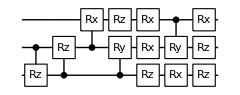

```mathematica
DrawCircuit[ansatz,qubitsnum]
```

```mathematica
θvars
```

<|θ_1→-1.57055,θ_2→1.57089,θ_4→-3.13788,θ_6→7.8531,θ_9→3.14136,θ_14→-4.71305,θ_18→1.57159,θ_19→1.57259,θ_31→0.391517,θ_32→1.57177,θ_41→2.36052,θ_49→0.784216,θ_50→-0.787139|>

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
conf["usecorr"]=False;
```

```mathematica
varMeanInitStates[conf]
```

<|1→{0.499845,0.21725},2→{0.400584,0.481403},3→{0.63785,0.117328},4→{0.155551,0.0725884}|>

```mathematica
CompileCirc[conf,unitary,qubitsnum]
```

Compilation with automatically generated ansatz

@cycle1:Mon 5 Sep 2022 10:48:20, fev:327, <E>: 0.27648542185718844 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 4, 12}

@cycle2:Mon 5 Sep 2022 10:48:55, fev:650, <E>: 0.17187658896734434 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 5, 18}

@cycle3:Mon 5 Sep 2022 10:49:29, fev:827, <E>: 0.12307780572161761 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 5, 23}

@cycle4:Mon 5 Sep 2022 10:50:07, fev:960, <E>: 0.11142053239730043 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 5, 27}

@cycle5:Mon 5 Sep 2022 10:51:00, fev:1122, <E>: 0.10468014523371248 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 5, 30}

@cycle6:Mon 5 Sep 2022 10:52:00, fev:1276, <E>: 0.10229838024360349 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 5, 33}

@cycle7:Mon 5 Sep 2022 10:52:57, fev:1377, <E>: 0.10134007403186936 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 6, 33}

@cycle8:Mon 5 Sep 2022 10:54:45, fev:1611, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 37}

I'm slowing down @cycle 9

@cycle9:Mon 5 Sep 2022 10:55:02, fev:1639, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 42}

I'm slowing down @cycle 10

@cycle10:Mon 5 Sep 2022 10:55:48, fev:1697, <E>: 0.10081847816131613 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 6, 51}

@cycle11:Mon 5 Sep 2022 10:59:52, fev:1859, <E>: 0.09690884571505695 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 49, 0, 6, 63}

@cycle12:Mon 5 Sep 2022 11:03:35, fev:1984, <E>: 0.09280713302435148 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 67, 0, 6, 82}

@cycle13:Mon 5 Sep 2022 11:07:09, fev:2122, <E>: 0.08987743863421298 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 90, 0, 6, 94}

$Aborted